```mathematica
rTab=Import["/Users/endres/Documents/MIT/research/bdeop/endres/su2/su2_v0.4/tests/Interpolator/matching.dat"];
```

```mathematica
rTab2=Import["/Users/endres/Documents/MIT/research/bdeop/endres/su2/su2_v0.4/tests/Interpolator/out.dat"];
```

```mathematica
rTab2=Drop[rTab2,2];
Min[rTab2]
```

0

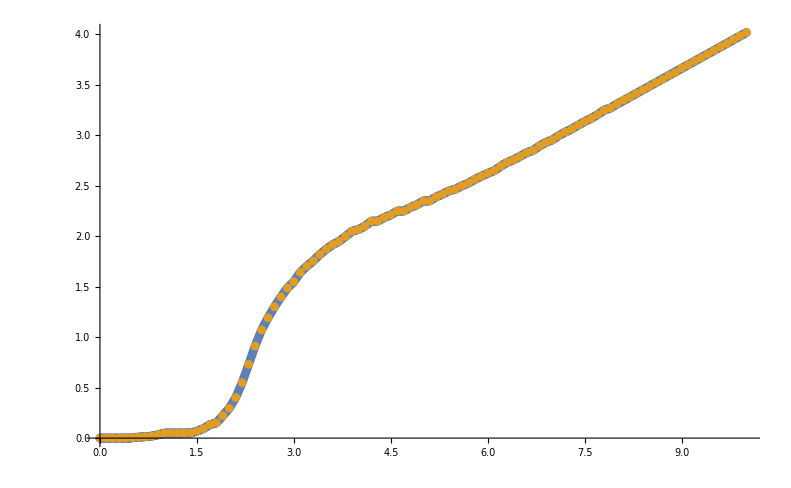

```mathematica
ListPlot[{rTab2,rTab},PlotStyle->{PointSize[0.008]},Joined->False]
```